Интерполационни сплайни - квадратичен сплайн

```mathematica
Clear[x,y,a,t,z,yy]
x={3,4.5,7,9};
y={2.5,1,2.5,0.5};
(*x={0.,1,2.,3.,4};   (* таблица за х *)
y={1.2,1.3,1.6,1.2,0.6}; (* таблица за у *)*)
n=Length[x]-1;
g1=ListPlot[Table[{x[[i]],y[[i]]},{i,1,n+1}],PlotStyle->Red];
a=b=c=y;
b[[1]]=0; (* естествен сплайн *)
For[i=1,i≤n,i++,
b[[i+1]]=-b[[i]]+2*(y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]]);
c[[i]]=(b[[i+1]]-b[[i]])/(2*(x[[i+1]]-x[[i]]))]
Print["Таблицата с квадратичните сплайни е:"]
For[k=1,k≤n,k++,
f[t_]:=a[[k]]+b[[k]]*(t-x[[k]])+c[[k]]*(t-x[[k]])^2;
Print["    интервал: [",x_⟦k⟧,";",x_⟦k+1⟧,"]   f[",k,"] = ",f[t]];
Print["f(t)= ",Collect[f[t],t]];
];
z=2.8;
For[j=1,j≤n,j++,
If[x[[j]]≤z&&z≤x[[j+1]],yy=a[[j]]+b[[j]]*(z-x[[j]])+c[[j]]*(z-x[[j]])^2]]
Print["Стойността на сплайна в точката x = ",z ," e ",yy]
g3=ListPlot[{{z,yy}},PlotStyle->Green];
```

Таблицата с квадратичните сплайни е:

интервал: [3;4.5]   f[1] = 2.5-0.666667 (-3+t)^2

f(t)= -3.5+4. t-0.666667 t^2

интервал: [4.5;7]   f[2] = 1-2. (-4.5+t)+1.04 (-4.5+t)^2

f(t)= 31.06-11.36 t+1.04 t^2

интервал: [7;9]   f[3] = 2.5+3.2 (-7+t)-2.1 (-7+t)^2

f(t)= -122.8+32.6 t-2.1 t^2

Стойността на сплайна в точката x = 2.8 e yy

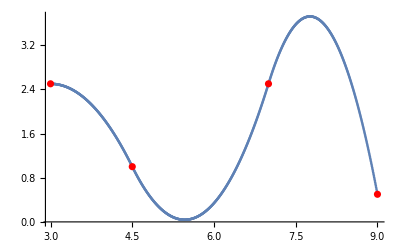

-Graphics-

```mathematica
(* графика на сплайна *)
np=1000;hh=(x_⟦n+1⟧-x_⟦1⟧)/np;
p={{x_⟦1⟧,y_⟦1⟧}};
For[i=1,i≤np,i++,xx=x_⟦1⟧+i*hh;
For[k=1,k≤n,k++,If[x_⟦k⟧≤xx && xx≤x_⟦k+1⟧,yy=a[[k]]+b[[k]]*(xx-x[[k]])+c[[k]]*(xx-x[[k]])^2];];
AppendTo[p,{xx,yy}];
];
g2=ListPlot[p];
Show[g2,g1,g3]
Show[g3]
```